```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1

### RK4

{{x→Function[{t},ArcTan[16 t]]}}

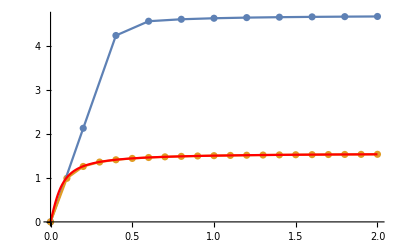

```mathematica
n10 = Import["./outputs/uloha1_RK4_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_RK4_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_RK4_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_RK4_80n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20}],
ListLinePlot[{n10, n20}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### RK2 vs RK4

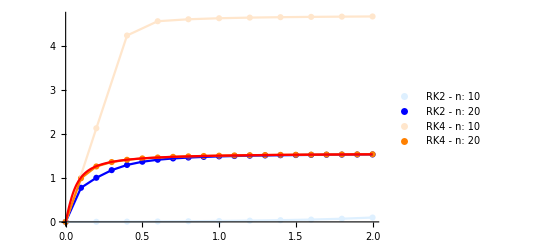

```mathematica
RK220 = Import["./outputs/uloha1_RK2_10n.csv","CSV"];
RK240 = Import["./outputs/uloha1_RK2_20n.csv","CSV"];
RK420 = Import["./outputs/uloha1_RK4_10n.csv","CSV"];
RK440 = Import["./outputs/uloha1_RK4_20n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{RK220, RK240, RK420, RK440}, PlotLegends->{"RK2 - n: 10", "RK2 - n: 20","RK4 - n: 10", "RK4 - n: 20"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
ListLinePlot[{RK220, RK240, RK420, RK440},PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 2

{{1/2,5/4},{1,1.99689},{3/2,3.24461},{2,4.99253}}

{{{1,2.02689},{2,4.0536}},{{3/2,3.26514},{5/2,6.27522}},{{2,5.00805},{3,9.01207}}}

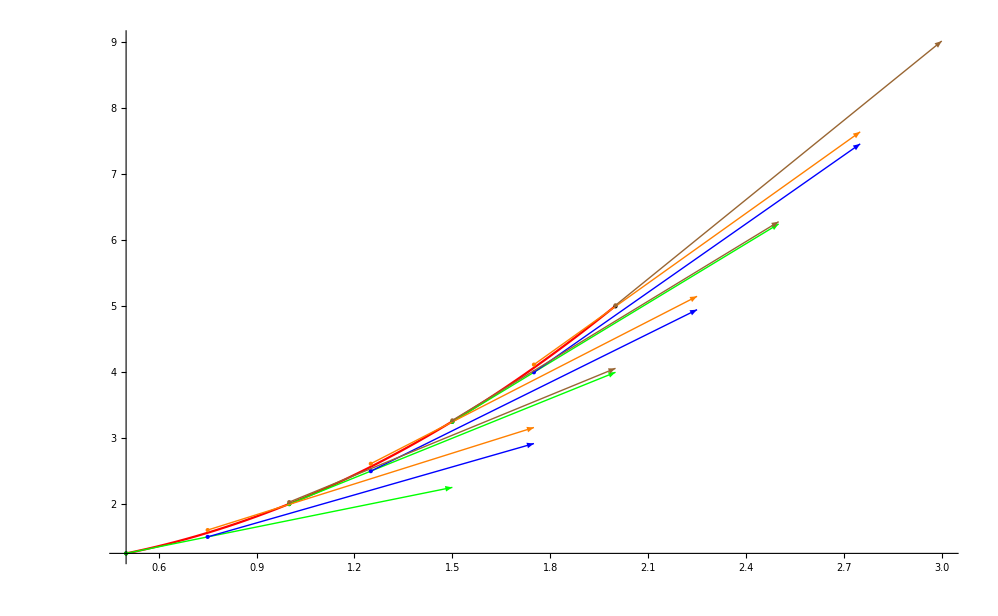

```mathematica
f[x_]:=2Sqrt[x-1];
x0 = 5/4;
t0=1/2;
t1 =2;
h=(t1-t0)/3;
approx={};
Y1={};
Y2={};
Y3={};
Y4={};
ui=x0;
For[i=0, i<4,i++,{
ti = t0 + i*h;
y1 = ui;
y2=ui+(h/2)*f[y1]//N;
y3=ui+(h/2)*f[y2]//N;
y4=ui+h*f[y3]//N;
If[i!=3,{
AppendTo[Y1, {ti,y1}];
AppendTo[Y2, {ti+h/2,y2}];
AppendTo[Y3, {ti+h/2,y3}];
AppendTo[Y4, {ti+h,y4}];
}];
AppendTo[approx,{ti, ui}];
ui+=(h/6)*(f[y1]+2*f[y2]+2*f[y3]+f[y4]) //N;
}]
approx
Table[{Y4[[i]],Y4[[i]]+{1,f[Y4[[i]][[2]]]} },{i,1,3}]
DSolve[{x'[t]==2Sqrt[x[t]-1], x[t0]==x0},x,{t,t0,t1}];
Show[{
Plot[Evaluate[x[t]/.%],{t,t0,t1}, PlotStyle->Red, PlotRange->All],
Graphics[{
Black,Point[approx], 
Green,Point[Y1],Arrow[Table[{Y1[[i]],Y1[[i]]+{1,f[Y1[[i]][[2]]]} },{i,1,3}]],
Blue, Point[Y2],Arrow[Table[{Y2[[i]],Y2[[i]]+{1,f[Y2[[i]][[2]]]} },{i,1,3}]],
Orange,Point[Y3],Arrow[Table[{Y3[[i]],Y3[[i]]+{1,f[Y3[[i]][[2]]]} },{i,1,3}]],
Brown, Point[Y4],Arrow[Table[{Y4[[i]],Y4[[i]]+{1,f[Y4[[i]][[2]]]} },{i,1,3}]]}]
}]
```

## Uloha 3

### Heu

{{x→Function[{t},√(-1+2 ⅇ^t)]}}

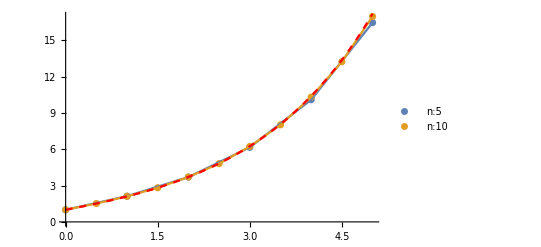

```mathematica
n5 = Import["./outputs/uloha3_heu_5n.csv","CSV"];
n10 = Import["./outputs/uloha3_heu_10n.csv","CSV"];
(*n20 = Import["./outputs/uloha3_heu_20n.csv","CSV"];
n40 = Import["./outputs/uloha3_heu_40n.csv","CSV"];
n80 = Import["./outputs/uloha3_heu_80n.csv","CSV"];*)
DSolve[{x'[t]==(x[t]^2+1)/(2x[t]), x[0]==1},x,{t,0,5}]
Show[
ListPlot[{n5, n10},PlotLegends->{"n:5", "n:10"}],
ListLinePlot[{n5, n10}],
Plot[Evaluate[x[t]/.%],{t,0,5}, PlotStyle->{Dashed, Red}, PlotRange->All]
]
```

### Heu vs Explicit Euler

{{x→Function[{t},√(-1+2 ⅇ^t)]}}

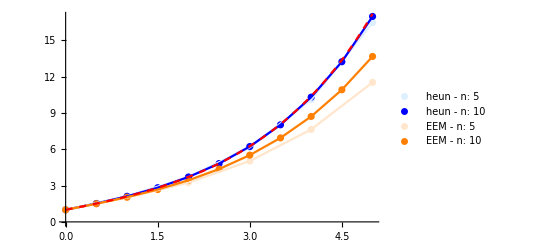

```mathematica
n5 = Import["./outputs/uloha3_heu_5n.csv","CSV"];
n10 = Import["./outputs/uloha3_heu_10n.csv","CSV"];
EE5 = Import["./outputs/uloha3_eul_5n.csv","CSV"];
EE10 = Import["./outputs/uloha3_eul_10n.csv","CSV"];
DSolve[{x'[t]==(x[t]^2+1)/(2x[t]), x[0]==1},x,{t,0,5}]
Show[
ListPlot[{n5, n10, EE5, EE10}, PlotLegends->{"heun - n: 5", "heun - n: 10","EEM - n: 5", "EEM - n: 10"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
ListLinePlot[{n5, n10, EE5, EE10},PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
Plot[Evaluate[x[t]/.%],{t,0,5}, PlotStyle->{Red, Dashed}, PlotRange->All]
]
```

## Uloha 4

```mathematica
Solve[{1+x /2 +(x)^2 /6+(x)^3/24 == 0}, x]
```

{{x→Root-2.79Root[24+12 #1+4 #1^2+#1^3&,1]-2.7852935634052813},{x→Root-0.607-2.87 ⅈRoot[24+12 #1+4 #1^2+#1^3&,2]-0.6073532182973577},{x→Root-0.607+2.87 ⅈRoot[24+12 #1+4 #1^2+#1^3&,3]-0.6073532182973577}}

```mathematica
Solve[{-1-x -(x)^2 /2-(x)^3/6-x^4/24 ==1}, x]
```

{{x→Root-2.22-1.69 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,1]-2.219446891977491},{x→Root-2.22+1.69 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,2]-2.219446891977491},{x→Root0.219-2.48 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,3]0.21944689197749137},{x→Root0.219+2.48 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,4]0.21944689197749137}}

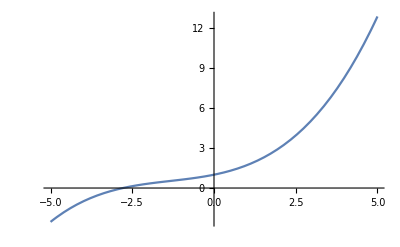

```mathematica
Plot[1+x /2 +(x)^2 /6+(x)^3/24, {x, -5, 5}]
```

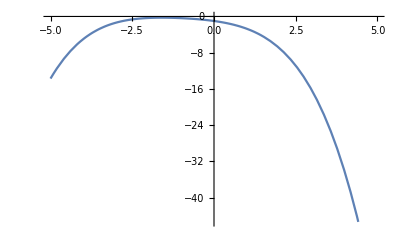

```mathematica
Plot[-1-x -(x)^2 /2-(x)^3/6-x^4/24, {x,-5,5}]
```